```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

SetDelayed::write: Tag Element in a_List∈{index___} is Protected.

dSVtShowInput::assm: Assumptions made: {b→0.75,F→0.94,s→0.08}.

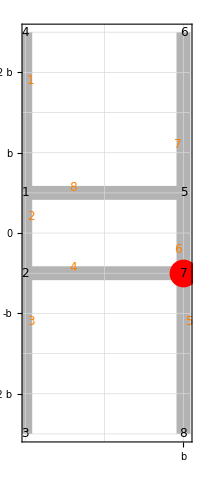

```mathematica
example={$$nodes->{{-b, b/2}, {-b, -1/2*b}, {-b, (-5*b)/2}, {-b, (5*b)/2}, {b, b/2}, {b, (5*b)/2}, {b, -1/2*b}, {b, (-5*b)/2}},
$$edges->{{4, 1}, {1, 2}, {2, 3}, {2, 7}, {7, 8}, {7, 5}, {5, 6}, {1, 5}},
$$thicknesses->s,$$absname->t,$$thname->z,
$$traction->F,$$wheretraction->{b, -b/2},
$$shear->{0, 0}, $$whereshear->{0, 0},
$$bending->{0,0}, $$torsion->0}; dSVtShowInput[example]
```

## Risultati

```mathematica
A=14b s;Iy=(34 b^3 s)/3;Ix=(131 b^3 s)/6;{a0,a1,a2}={F/(14 b s),(3 F)/(34 b^2 s),-(3 F)/(131 b^2 s)};
rhox2=Ix/A;rhoy2=Iy/A;
σ[x_,y_]=a0-a1*x-a2*y;
σmax=σ[b,-5/2 b]//FullSimplify
σmin=σ[-b,5/2 b]//FullSimplify
```

-(2309 F)/(31178 b s)

(6763 F)/(31178 b s)

### Versione 1

```mathematica
valori1={γ->20*Pi/180,F->Quantity[2*10^4,"Kilonewtons"],b->Quantity[12,"Centimeters"],s->Quantity[1,"Centimeters"],σ0->Quantity[20,"Kilonewtons"/"Centimeters"^2]};
risultati1={A,Ix,Iy,β,σmax,σmin,σmax/σ0,σmin/σ0}/.valori1//N//NumberForm[#,3]&
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

{168. cm^2,37700. cm^4,19600. cm^4,β,-123. kN/cm^2,362. kN/cm^2,-6.17,18.1}

### Versione 2

```mathematica
valori2={γ->80*Pi/180,MM->Quantity[5*10^4,"KiMlonewtons"*"Centimeters"],b->Quantity[14,"Centimeters"],s->Quantity[1,"Centimeters"],σ0->Quantity[20,"Kilonewtons"/"Centimeters"^2]};
risultati2={A,Ix,Iy,β,σmax,σmin,σmax/σ0,σmin/σ0}/.valori2//N//NumberForm[#,3]&
```

Quantity::unkunit: Unable to interpret unit specification Centimeters KiMlonewtons.

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

{196. cm^2,59900. cm^4,31100. cm^4,β,F (-0.00529 /cm^2),F (0.0155 /cm^2),F (-0.000264 /kN),F (0.000775 /kN)}

## Output simbolico

Evaluate the following cell to solve the problem and see the output

```mathematica
sol = {AB, rG, JB, CS, FS, KT, sigma, tau, gobj, details} = dSVtSolve[example];
gsol=dSVtShowOutput[example, sol]
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

123456

Evaluate the following cell to print the above output

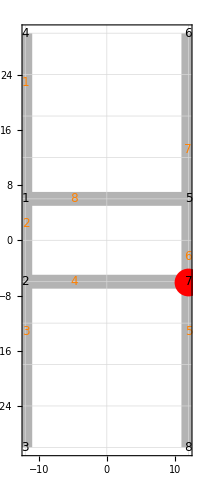

-Graphics-

-Graphics-

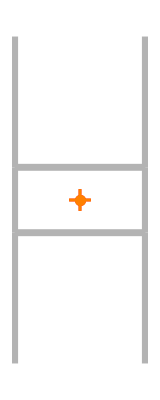

-Graphics-

-Graphics-

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Numerical assumptions for visualization purposes

{b→0.75,F→0.94,s→0.08}

Edge lengths

{{2 b,b,2 b,2 b,2 b,b,2 b,2 b}}

Edges areas Ai

{{2 b s,b s,2 b s,2 b s,2 b s,b s,2 b s,2 b s}}

Total area A

14 b s

Edges static moments sPi

{{{-2 b^2 s,3 b^2 s},{-b^2 s,0},{-2 b^2 s,-3 b^2 s},{0,-b^2 s},{2 b^2 s,-3 b^2 s},{b^2 s,0},{2 b^2 s,3 b^2 s},{0,b^2 s}}}

Static moment sP

{{0,0}}

Edge centroids Gi

{{{-b,(3 b)/2},{-b,0},{-b,-(3 b)/2},{0,-b/2},{b,-(3 b)/2},{b,0},{b,(3 b)/2},{0,b/2}}}

Centroid G

{{0,0}}

Edges Euler inertia tensors IPi

{{{{2 b^3 s,-3 b^3 s},{-3 b^3 s,(31 b^3 s)/6}},{{b^3 s,0},{0,(b^3 s)/12}},{{2 b^3 s,3 b^3 s},{3 b^3 s,(31 b^3 s)/6}},{{(2 b^3 s)/3,0},{0,(b^3 s)/2}},{{2 b^3 s,-3 b^3 s},{-3 b^3 s,(31 b^3 s)/6}},{{b^3 s,0},{0,(b^3 s)/12}},{{2 b^3 s,3 b^3 s},{3 b^3 s,(31 b^3 s)/6}},{{(2 b^3 s)/3,0},{0,(b^3 s)/2}}}}

Total Euler inertia tensor IP

{{(34 b^3 s)/3,0},{0,(131 b^3 s)/6}}

Inertia tensor after translation in the centroid IG

{{(34 b^3 s)/3,0},{0,(131 b^3 s)/6}}

Principal inertia momoments (jI, jII) and associated directions

{{(34 b^3 s)/3,{0,1}},{(131 b^3 s)/6,{1,0}}}

Rotation to principal directions

0

Radii of gyration (ρI, ρII)

{{√(17/21) b,1/2 √(131/21) b}}

Section moduli (WI, WII) and associated directions

{{{(68 b^2 s)/15,(68 b^2 s)/15},{0,1}},{{(131 b^2 s)/6,(131 b^2 s)/6},{1,0}}}

Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2)

{F/(14 b s),(3 F)/(34 b^2 s),-(3 F)/(131 b^2 s)}

Sigma in principal axis (ξ,η)

((-0.0229008 "η"+0.0882353 "ξ"+0.0714286 b) F)/(b^2 s)

Neutral axis for sigma

{x1→-(17 b)/21+(34 x2)/131}

Intersections of neutral axis with principal axis

{Last[{}],Last[{}]}

Inertia ellipse equation

((21 x1^2)/17+(84 x2^2)/131)/b^2==2

Kern (Convex hull (convex hull has been computed on a numerical instance!)

{{-(17 b)/21,0},{-(17 b)/21,0},{-(17 b)/21,0},{0,-(131 b)/210},{(17 b)/21,0},{(17 b)/21,0},{(17 b)/21,0},{0,(131 b)/210}}

(Shear) Cycles in terms of nodes

{{5,1,2,7,5}}

(Shear) Cycles in terms of edges

{{-8,2,4,6}}

Associated open graph {nodes, edges} (statically undetermined shear)

{{{-b,b/2},{-b,-b/2},{-b,-(5 b)/2},{-b,(5 b)/2},{b,b/2},{b,(5 b)/2},{b,-b/2},{b,-(5 b)/2},{b,b/2}},{{4,1},{1,2},{2,3},{2,7},{7,8},{7,5},{5,6},{1,9}}}

Jourawsky shear on the associated open graph (statically undetermined shear)

{0,0,0,0,0,0,0,0}

Cycles connectivity

{{0},{1},{0},{1},{0},{1},{0},{-1}}

Congruence for statically undetermined shear, matrix ηij

{{(6 b)/s}}

Congruence for statically undetermined shear, vector η0i

{0}

Statically undetermined shear solution: Prandtl function values

{0}

Statically undetermined shear solution: shear fluxes

{0,0,0,0,0,0,0,0}

Shear stress if the shear force is placed in the shear center

{0,0,0,0,0,0,0,0}

Shear stiffness matrix

{{5780/27111,0},{0,17161/29778}}

Shear flexibility matrix

{{27111/5780,0},{0,29778/17161}}

Shear resultants on edges

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}

Shear resultant

{0,0}

Shear center

{{0,0}}

Additional torque due to eccentricity

0

(Torsion) Cycles in terms of nodes

{{5,1,2,7}}

(Torsion) Cycles in terms of edges

{{-8,2,4,6}}

Statically undetermined torsion, congruence matrix ηij

{{(6 b)/s}}

Statically undetermined torsion, vector  2Ω

{4 b^2}

Solution of the statically undetermined torsion

{(2 b s)/3}

Torsion partition over the cycles  Ji/J

{1}

Shear stress due to torsion

{{0,0,0,0,0,0,0,0}}

Torsional inertias Jti

{{{8,2,4,6},(8 b^3 s)/3},{1,(2 b s^3)/3},{3,(2 b s^3)/3},{5,(2 b s^3)/3},{7,(2 b s^3)/3}}

Torsional inertia Jt

8/3 b s (b^2+s^2)

-Graphics-

-Graphics-

-Graphics-

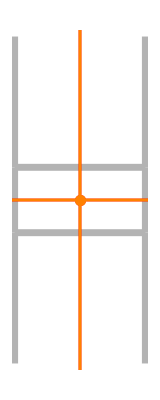

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Output
```

Output

## Output numerico

Evaluate the following cell to solve the problem and see the output

```mathematica
b=12;s=1;F=2*10^4;
sol = {AB, rG, JB, CS, FS, KT, sigma, tau, gobj, details} = dSVtSolve[example];
gsol=dSVtShowOutput[example, sol]
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

123456

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Numerical assumptions for visualization purposes

{}

Edge lengths

{{24,12,24,24,24,12,24,24}}

Edges areas Ai

{{24,12,24,24,24,12,24,24}}

Total area A

168

Edges static moments sPi

{{{-288,432},{-144,0},{-288,-432},{0,-144},{288,-432},{144,0},{288,432},{0,144}}}

Static moment sP

{{0,0}}

Edge centroids Gi

{{{-12,18},{-12,0},{-12,-18},{0,-6},{12,-18},{12,0},{12,18},{0,6}}}

Centroid G

{{0,0}}

Edges Euler inertia tensors IPi

{{{{3456,-5184},{-5184,8928}},{{1728,0},{0,144}},{{3456,5184},{5184,8928}},{{1152,0},{0,864}},{{3456,-5184},{-5184,8928}},{{1728,0},{0,144}},{{3456,5184},{5184,8928}},{{1152,0},{0,864}}}}

Total Euler inertia tensor IP

{{19584,0},{0,37728}}

Inertia tensor after translation in the centroid IG

{{19584,0},{0,37728}}

Principal inertia momoments (jI, jII) and associated directions

{{19584,{0,1}},{37728,{1,0}}}

Rotation to principal directions

0

Radii of gyration (ρI, ρII)

{{4 √(51/7),2 √(393/7)}}

Section moduli (WI, WII) and associated directions

{{{3264/5,3264/5},{0,1}},{{3144,3144},{1,0}}}

Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2)

{2500/21,625/51,-1250/393}

Sigma in principal axis (ξ,η)

119.048-3.18066 "η"+12.2549 "ξ"

Neutral axis for sigma

{x1→-68/7+(34 x2)/131}

Intersections of neutral axis with principal axis

{Last[{}],Last[{}]}

Inertia ellipse equation

(7 x1^2)/816+(7 x2^2)/1572==2

Kern (Convex hull (convex hull has been computed on a numerical instance!)

{{-68/7,0},{-68/7,0},{-68/7,0},{0,-262/35},{68/7,0},{68/7,0},{68/7,0},{0,262/35}}

(Shear) Cycles in terms of nodes

{{5,1,2,7,5}}

(Shear) Cycles in terms of edges

{{-8,2,4,6}}

Associated open graph {nodes, edges} (statically undetermined shear)

{{{-12,6},{-12,-6},{-12,-30},{-12,30},{12,6},{12,30},{12,-6},{12,-30},{12,6}},{{4,1},{1,2},{2,3},{2,7},{7,8},{7,5},{5,6},{1,9}}}

Jourawsky shear on the associated open graph (statically undetermined shear)

{0,0,0,0,0,0,0,0}

Cycles connectivity

{{0},{1},{0},{1},{0},{1},{0},{-1}}

Congruence for statically undetermined shear, matrix ηij

{{72}}

Congruence for statically undetermined shear, vector η0i

{0}

Statically undetermined shear solution: Prandtl function values

{0}

Statically undetermined shear solution: shear fluxes

{0,0,0,0,0,0,0,0}

Shear stress if the shear force is placed in the shear center

{0,0,0,0,0,0,0,0}

Shear stiffness matrix

{{5780/27111,0},{0,17161/29778}}

Shear flexibility matrix

{{27111/5780,0},{0,29778/17161}}

Shear resultants on edges

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}

Shear resultant

{0,0}

Shear center

{{0,0}}

Additional torque due to eccentricity

0

(Torsion) Cycles in terms of nodes

{{5,1,2,7}}

(Torsion) Cycles in terms of edges

{{-8,2,4,6}}

Statically undetermined torsion, congruence matrix ηij

{{72}}

Statically undetermined torsion, vector  2Ω

{576}

Solution of the statically undetermined torsion

{8}

Torsion partition over the cycles  Ji/J

{1}

Shear stress due to torsion

{{0,0,0,0,0,0,0,0}}

Torsional inertias Jti

{{{8,2,4,6},4608},{1,8},{3,8},{5,8},{7,8}}

Torsional inertia Jt

4640

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Output
```

Output

## Output numerico versione 2

Evaluate the following cell to solve the problem and see the output

```mathematica
γ=80*Pi/180;MM=3*10^4;b=14;s=1;
sol = {AB, rG, JB, CS, FS, KT, sigma, tau, gobj, details} = dSVtSolve[example];
gsol=dSVtShowOutput[example, sol]
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

123456

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Numerical assumptions for visualization purposes

{}

Edge lengths

{{28,14,28,28,28,14,28,28}}

Edges areas Ai

{{28,14,28,28,28,14,28,28}}

Total area A

196

Edges static moments sPi

{{{-392,588},{-196,0},{-392,-588},{0,-196},{392,-588},{196,0},{392,588},{0,196}}}

Static moment sP

{{0,0}}

Edge centroids Gi

{{{-14,21},{-14,0},{-14,-21},{0,-7},{14,-21},{14,0},{14,21},{0,7}}}

Centroid G

{{0,0}}

Edges Euler inertia tensors IPi

{{{{5488,-8232},{-8232,42532/3}},{{2744,0},{0,686/3}},{{5488,8232},{8232,42532/3}},{{5488/3,0},{0,1372}},{{5488,-8232},{-8232,42532/3}},{{2744,0},{0,686/3}},{{5488,8232},{8232,42532/3}},{{5488/3,0},{0,1372}}}}

Total Euler inertia tensor IP

{{93296/3,0},{0,179732/3}}

Inertia tensor after translation in the centroid IG

{{93296/3,0},{0,179732/3}}

Principal inertia momoments (jI, jII) and associated directions

{{93296/3,{0,1}},{179732/3,{1,0}}}

Rotation to principal directions

0

Radii of gyration (ρI, ρII)

{{2 √(119/3),√(917/3)}}

Section moduli (WI, WII) and associated directions

{{{13328/15,13328/15},{0,1}},{{12838/3,12838/3},{1,0}}}

Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2)

{5000/49,7500/833,-15000/6419}

Sigma in principal axis (ξ,η)

102.041-2.33681 "η"+9.0036 "ξ"

Neutral axis for sigma

{x1→-34/3+(34 x2)/131}

Intersections of neutral axis with principal axis

{Last[{}],Last[{}]}

Inertia ellipse equation

(3 x1^2)/476+(3 x2^2)/917==2

Kern (Convex hull (convex hull has been computed on a numerical instance!)

{{-34/3,0},{-34/3,0},{-34/3,0},{0,-131/15},{34/3,0},{34/3,0},{34/3,0},{0,131/15}}

(Shear) Cycles in terms of nodes

{{5,1,2,7,5}}

(Shear) Cycles in terms of edges

{{-8,2,4,6}}

Associated open graph {nodes, edges} (statically undetermined shear)

{{{-14,7},{-14,-7},{-14,-35},{-14,35},{14,7},{14,35},{14,-7},{14,-35},{14,7}},{{4,1},{1,2},{2,3},{2,7},{7,8},{7,5},{5,6},{1,9}}}

Jourawsky shear on the associated open graph (statically undetermined shear)

{0,0,0,0,0,0,0,0}

Cycles connectivity

{{0},{1},{0},{1},{0},{1},{0},{-1}}

Congruence for statically undetermined shear, matrix ηij

{{84}}

Congruence for statically undetermined shear, vector η0i

{0}

Statically undetermined shear solution: Prandtl function values

{0}

Statically undetermined shear solution: shear fluxes

{0,0,0,0,0,0,0,0}

Shear stress if the shear force is placed in the shear center

{0,0,0,0,0,0,0,0}

Shear stiffness matrix

{{5780/27111,0},{0,17161/29778}}

Shear flexibility matrix

{{27111/5780,0},{0,29778/17161}}

Shear resultants on edges

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}

Shear resultant

{0,0}

Shear center

{{0,0}}

Additional torque due to eccentricity

0

(Torsion) Cycles in terms of nodes

{{5,1,2,7}}

(Torsion) Cycles in terms of edges

{{-8,2,4,6}}

Statically undetermined torsion, congruence matrix ηij

{{84}}

Statically undetermined torsion, vector  2Ω

{784}

Solution of the statically undetermined torsion

{28/3}

Torsion partition over the cycles  Ji/J

{1}

Shear stress due to torsion

{{0,0,0,0,0,0,0,0}}

Torsional inertias Jti

{{{8,2,4,6},21952/3},{1,28/3},{3,28/3},{5,28/3},{7,28/3}}

Torsional inertia Jt

22064/3

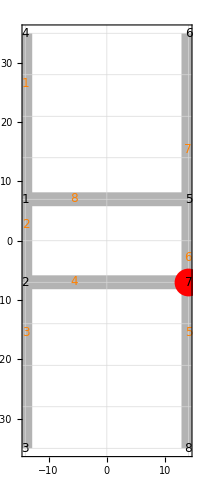

-Graphics-

-Graphics-

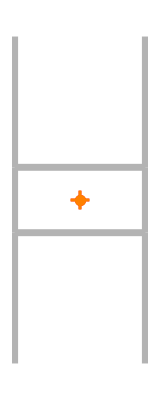

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Output
```

Output